## Lagrangian EOM VH

```mathematica
(*This is for the template*)
q={ζ[t]};
dq=D[q,t];
ddq=D[dq,t];
(*for analysis*)
(*KE=1/2m ζ0 ^2D[q,t].D[q,t];*)
(*[Seipel (2007)] (1)*)
L2=ζ'[t]^2/2-kt/2(1-ζ[t])^2;

Llhs=(D[D[L2,{dq}],t]-D[L2,{q}]//Simplify)
(*Coefficient[Llhs,ζ''[t]]*)
```

{-kt+kt ζ[t]+ζ''[t]}

#### Anchor with MSD

```mathematica
(*Anchor: MSD with refl act prop*)
(*Find M, C, g etc. and check against Lagrangian*)
M={{(m+ma/τ^2) ζ0^2}};
Cc={{0}};
(*how does act stiffness appear??*)
gg={m g/gt(-1+ζ[t])+(ka/τ^2)ζ0^2 ζ[t]};
lhs=M.ddq+Cc.dq+gg;

(*Find H*)
pbt={ζ0^2 (m+ma/τ^2),ka ζ0^2/τ^2};
MdqT=M.dq
(*pbt=Join[pb,{1/τ^2}];*)
HMqT={{ζ'[t],0}};
Print["HMqT =",HMqT//MatrixForm," check ",MdqT-HMqT.pbt//Simplify]
(*1st order*)
CgJ=(Cc+{{bζ ζ0}}).dq+gg(*MISSING J F*)
CgJT=CgJ+{ba/τ^2 dσo+ka/τ^2 σo};
HCgJT={{0,ζ[t]}};
Print["HCgJ =",HCgJT//MatrixForm," check ",CgJT-HCgJT.pbt//Simplify]
```

{ζ0^2 (m+ma/τ^2) ζ'[t]}

HMqT =(ζ'[t] | 0) check {0}

{(g m (-1+ζ[t]))/gt+(ka ζ0^2 ζ[t])/τ^2+bζ ζ0 ζ'[t]}

HCgJ =(0 | ζ[t]) check {(ba dσo)/τ^2+(ka σo)/τ^2+(g m (-1+ζ[t]))/gt+bζ ζ0 ζ'[t]}

#### Anchor with full linkage with non-parallel 4bar?

## Lagrangian EOM W2D

```mathematica
q={σ[t],ψ[t]};
dq=D[q,t];
(*for analysis*)
pwing={σ[t],0}+RotationMatrix[ψ[t]].{0,-γ cbar};
Iwing=mwing (γ cbar)^2;
KE=(*1/2mspar σ'[t]^2+*)1/2Iwing ψ'[t]^2+1/2mwing D[pwing,t].D[pwing,t];
L2=KE-(1/2 kψ ψ[t]^2+1/2kσ σ[t]^2);
(*paero2=({ϕ[t],0}+RotationMatrix[ψ[t]].{0,-cbar/2});
Faero2W={FL,FD};
τaero2=-D[paero2,{{ϕ[t],ψ[t]}}]ᵀ.Faero2W;*)

Llhs=(D[D[L2,{dq}],t]-D[L2,{q}](*+τaero2*)//Simplify)
Coefficient[Llhs,σ''[t]]
Coefficient[Llhs,ψ''[t]]
```

{kσ σ[t]+mwing (-cbar γ Sin[ψ[t]] ψ'[t]^2+σ''[t]+cbar γ Cos[ψ[t]] ψ''[t]),kψ ψ[t]+cbar mwing γ (Cos[ψ[t]] σ''[t]+2 cbar γ ψ''[t])}

{mwing,cbar mwing γ Cos[ψ[t]]}

{cbar mwing γ Cos[ψ[t]],2 cbar^2 mwing γ^2}

## Find H

```mathematica
dq={T dσa,dψ};
ddq={T ddσa,ddψ};
Iw=mw cb^2;
M={{mw,cb γ mw Cos[ψ]},{cb γ mw Cos[ψ],2cb^2γ^2mw}};Cc={{0,-cb mw Sin[ψ]dψ},{0,0}};
gg={kσ (T σa),kψ ψ};
lhs=M.ddq+Cc.dq+gg
(*p={cb,T};
lhs//MatrixForm
(Dlp=D[lhs,{p}])//MatrixForm
lhs-(Dlp.p)//Simplify
(*Did this by hand TODO automate this somehow*)
Htest={
{0,dσa(mw)+kσ σa,mw (ddψ Cos[ψ]-dψ^2Sin[ψ]),0,0},
{kψ ψ+Iw ddψ,0,0,mw ddσa Cos[ψ],mw ddψ}
};
Htest//MatrixForm
pb={1,T,cb,cb T,cb^2};
lhs-Htest.pb//Simplify*)
```

{ddσa mw T+kσ T σa+cb ddψ mw γ Cos[ψ]-cb dψ^2 mw Sin[ψ],2 cb^2 ddψ mw γ^2+kψ ψ+cb ddσa mw T γ Cos[ψ]}

```mathematica
(*(*pieces from notes*)
Mdq=M.dq;
HMq={{0,dσa (mw),dψ mw Cos[ψ],0,0},{dψ Iw,0,0,dσa mw Cos[ψ],dψ mw}};
Print["HMq =",HMq//MatrixForm," check ",Mdq-HMq.pb//Simplify]
CgJ=(Ccᵀ-DiagonalMatrix[{bσ,bψ}]).dq-gg;(*MISSING J F*)
HCgJ={{0,-kσ σa-bσ dσa,0,0,0},{-kψ ψ-bψ dψ,0,0,- dσa dψ mw Sin[ψ],0}};
Print["HCgJ =",HCgJ//MatrixForm," check ",CgJ-HCgJ.pb//Simplify]*)
```

```mathematica
(*(*Another version for 1st order integration - see notes*)
HCgJ={{0,kσ σa+bσ dσa,-dψ^2 mw Sin[ψ],0,0},{kψ ψ+bψ dψ,0,0,0,0}};
CgJ=(Cc+DiagonalMatrix[{bσ,bψ}]).dq+gg;(*MISSING J F*)
Print["HCgJ =",HCgJ//MatrixForm," check ",CgJ-HCgJ.pb//Simplify]*)
```

### Output coords

```mathematica
dq={dσo,dψ};
ddq={ddσo,ddψ};
gg={kσ σo,kψ ψ};
lhs=M.ddq+Cc.dq+gg;
p={cb,T};
(*Did this by hand TODO automate this somehow*)
Htest={
{kσ σo,0,0,0,ddσo,(γ ddψ Cos[ψ]-dψ^2Sin[ψ]),0},
{0,ψ,0,0,0,γ ddσo Cos[ψ],2ddψ γ^2}(*the 2ddψ corresponds to Iw+mw cb^2*)
};
Htest//MatrixForm
pb={1,kψ,bψ,cb,mw,mw cb,mw cb^2};
lhs-Htest.pb//Simplify
```

(kσ σo | 0 | 0 | 0 | ddσo | ddψ γ Cos[ψ]-dψ^2 Sin[ψ] | 0
0 | ψ | 0 | 0 | 0 | ddσo γ Cos[ψ] | 2 ddψ γ^2)

{0,0}

```mathematica
(*pieces from notes*)
Mdq=M.dq;
HMq={{0,0,0,0,dσo ,γ dψ Cos[ψ],0},
{0,0,0,0,0,γ dσo Cos[ψ],2γ^2 dψ}};(*the 2ddψ corresponds to Iw+mw cb^2*)
Print["HMq =",HMq//MatrixForm," check ",Mdq-HMq.pb//Simplify]
(*CgJ=(Ccᵀ-DiagonalMatrix[{bσ,bψ}]).dq-gg;(*MISSING J F*)
HCgJ={{-kσ σo-bσ dσo,0,0,0},
{-kψ ψ-bψ dψ,0,- dσo dψ Sin[ψ],0}};
Print["HCgJ =",HCgJ//MatrixForm," check ",CgJ-HCgJ.pb//Simplify]*)
(*Another version for 1st order integration - see notes*)
CgJ=(Cc+DiagonalMatrix[{bσ,bψ}]).dq+gg;(*MISSING J F*)
HCgJ={{kσ σo+bσ dσo,0,0,0,0,-dψ^2 Sin[ψ],0},
{0,ψ,dψ,0,0,0,0}};
Print["HCgJ =",HCgJ//MatrixForm," check ",CgJ-HCgJ.pb//Simplify]
```

HMq =(0 | 0 | 0 | 0 | dσo | dψ γ Cos[ψ] | 0
0 | 0 | 0 | 0 | 0 | dσo γ Cos[ψ] | 2 dψ γ^2) check {0,0}

HCgJ =(bσ dσo+kσ σo | 0 | 0 | 0 | 0 | -dψ^2 Sin[ψ] | 0
0 | ψ | dψ | 0 | 0 | 0 | 0) check {0,0}

### With reflected actuator properties

```mathematica
MdqT=Mdq+{ma/τ^2 dσo,0};
pbt=Join[pb,{1/τ^2}];
HMqT=ArrayFlatten[{{HMq,{{ma dσo},{0}}}}];
Print["HMqT =",HMqT//MatrixForm," check ",MdqT-HMqT.pbt//Simplify]
(*1st order*)
CgJT=CgJ+{ba/τ^2 dσo+ka/τ^2 σo,0};
HCgJT=ArrayFlatten[{{HCgJ,{{ba dσo+ka σo},{0}}}}];
Print["HCgJ =",HCgJT//MatrixForm," check ",CgJT-HCgJT.pbt//Simplify]
```

HMqT =(0 | 0 | 0 | 0 | dσo | dψ γ Cos[ψ] | 0 | dσo ma
0 | 0 | 0 | 0 | 0 | dσo γ Cos[ψ] | 2 dψ γ^2 | 0) check {0,0}

HCgJ =(bσ dσo+kσ σo | 0 | 0 | 0 | 0 | -dψ^2 Sin[ψ] | 0 | ba dσo+ka σo
0 | ψ | dψ | 0 | 0 | 0 | 0 | 0) check {0,0}

### H unactuated DOFs

```mathematica
H2={ψ,dψ,rcop(F1 Cos[ψ]+F2 Sin[ψ]),γ Cos[ψ](dσn-dσ)/δ,2γ^2(dψn-dψ)/δ};
H2b=H2/.{ψ->ψ+ϵ Δψ,dψ->dψ+ϵ Δdψ,σ->σ+ϵ Δσ,dσ->dσ+ϵ Δdσ,dσn->dσn+ϵ Δdσn,dψn->dψn+ϵ Δdψn};
Normal@Series[H2b-H2,{ϵ,0,1}]
```

{Δψ ϵ,Δdψ ϵ,rcop ϵ (F2 Δψ Cos[ψ]-F1 Δψ Sin[ψ]),(γ ϵ ((-Δdσ+Δdσn) Cos[ψ]-(-dσ+dσn) Δψ Sin[ψ]))/δ,(2 γ^2 (-Δdψ+Δdψn) ϵ)/δ}

## From Kevin paper

```mathematica
c16Tab1={(*spar width (mm)*) {0.14, 0.17, 0.20, 0.23, 0.26, 0.29}, 
(*Ixx(mg·mm2)*) {1.91, 2.25, 2.56, 2.90, 3.27, 3.64},
(* Izz(mg·mm2)*) {40.6, 48.8, 57.2, 65.6, 73.4, 82.7}}ᵀ;
(*Try to predict based on some density *)
(*Chen 2016 JFM paper: The wing weighs 0.52 mg,has a wing span of 12.8 mm and a surface area of 54 mm2.The origin of the coordinate system is located at the wing tip leading edge.The centre of mass is located at x=3.41 mm,y=−0.52 mm,z=−0.04 mm.The moments of inertia Ixx,Iyy and Izz with respect to the centre of mass are 1.54,18.78 and 20.0 mg mm2*)
IPredict=Table[
Module[{dspar=c16Tab1[[i,1]],ar=54,ρmem},
{dspar,0.2+11.5dspar,290dspar}
],{i,Length[c16Tab1]}]
ListPointPlot3D[{c16Tab1[[;;,;;]],IPredict},Filling->Bottom,AxesLabel->{"spar width (mm)","Ixx(mg·mm2)","Izz(mg·mm2)"}]
```

{{0.14,1.81,40.6},{0.17,2.155,49.3},{0.2,2.5,58.},{0.23,2.845,66.7},{0.26,3.19,75.4},{0.29,3.535,84.1}}

-Graphics3D-

## Nonlinear transmission modeling

```mathematica
(*Some versions*)
Solve[lt^2-l2^2==l2^2+(lt-σa)^2-2l2 (lt-σa) Cos[π/2-θo],θo]
Solve[lt^2+l2^2==l2^2+(lt-σa)^2-2l2 (lt-σa) Cos[π/2-θo],θo]
Solve[(l1-σa)^2==l2^2+lt^2-2l2 lt Cos[π/2-θo],θo]/.l1->Sqrt[lt^2-l2^2]

scθo1[lt_,l2_,σa_]:=ArcSin[(2 l2^2-2 lt σa+σa^2)/(2 l2 (lt-σa))]
scθo2[lt_,l2_,σa_]:=ArcSin[(-2 lt σa+σa^2)/(2 l2 (lt-σa))]
scθo3[lt_,l2_,σa_]:=ArcSin[(2 lt^2+2 √(l2^2-lt^2) σa-σa^2)/(2 l2 lt)]
params={l2->1.5,lt->5,l3->5};
Manipulate[
Graphics[
Module[{θo,p1={σa,0},p2,p3},
θo=scθo1[lt,l2,σa];
p2={lt,0}+l2{-Sin[θo],Cos[θo]};
p3={lt,0}-l3{-Sin[θo],Cos[θo]};
{
Thick,
Line[{{0,0},p1,p2,p3}],
Text[Norm[p1-p2],{-2,-2}]
}
],
GridLines->Automatic,
PlotRange->{{-10,10},{-10,10}}
]/.params,
{{σa,0},-1,1}]
```

{{θo→ConditionalExpression[π-ArcSin[(2 l2^2-2 lt σa+σa^2)/(2 l2 (lt-σa))]+2 π C[1],C[1]∈ℤ]},{θo→ConditionalExpression[ArcSin[(2 l2^2-2 lt σa+σa^2)/(2 l2 (lt-σa))]+2 π C[1],C[1]∈ℤ]}}

{{θo→ConditionalExpression[π-ArcSin[(-2 lt σa+σa^2)/(2 l2 (lt-σa))]+2 π C[1],C[1]∈ℤ]},{θo→ConditionalExpression[ArcSin[(-2 lt σa+σa^2)/(2 l2 (lt-σa))]+2 π C[1],C[1]∈ℤ]}}

{{θo→ConditionalExpression[π-ArcSin[(2 l2^2+2 √(-l2^2+lt^2) σa-σa^2)/(2 l2 lt)]+2 π C[1],C[1]∈ℤ]},{θo→ConditionalExpression[ArcSin[(2 l2^2+2 √(-l2^2+lt^2) σa-σa^2)/(2 l2 lt)]+2 π C[1],C[1]∈ℤ]}}

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

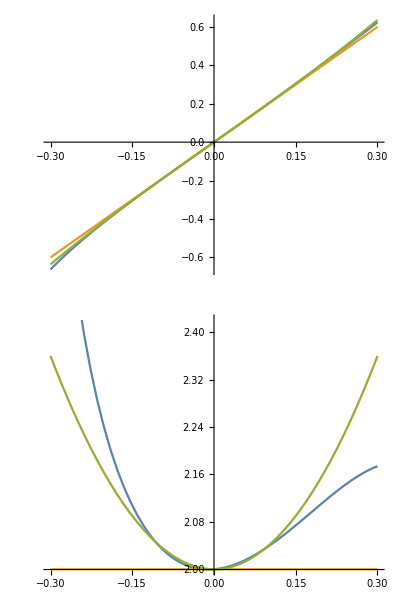

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*More Robobee-like*)
p1={σa,0};
p2={l2,l1};
p3=p2+RotationMatrix[θo].{l2o,-l1o};
θorb0=θo/.Last@Solve[(p3-p1).(p3-p1)==(l2+l2o)^2,θo]/.C[1]->0//Simplify;
params={l1->0.5,l2->0.5,l1o->0.5,l2o->0.01,τ1->2,τ2->4};
σalim=0.3;
Row@{
Manipulate[
Graphics[
Module[{},
{
Thick,
Line[{p1,p3}],
Line[{p2,p2+RotationMatrix[θo].{10,0}}],
Line[{p3,p2+RotationMatrix[θo].{l2o,0}}],
Dashed,
Line[{p1,p2,p3}],
Text[N@Norm[p1-p3],{-0.1,-0.1}]
}/.θo->θorb0/.σa->σaa
],
GridLines->Automatic,ImageSize->300,
PlotRange->{{-1,5},{-2,2}}
]/.params,
{{σaa,0},-σalim,σalim}],
(*Analytical*)
Module[{ss,ss0=0,Ds,Ds0},
ss=θorb0;
Ds=D[θorb0,σa]//Simplify;
Ds0=Ds/.σa->0;
Column@{
Plot[Evaluate[{ss-ss0,Ds0 σa,τ1 σa+τ2 σa^3/3}/.params],{σa,-σalim,σalim},ImageSize->Small],
Plot[Evaluate[{Ds,Ds0,τ1+τ2 σa^2}/.params],{σa,-σalim,σalim},ImageSize->Small]
}
]
}
```

```mathematica
(*Inverse of the transmission function*)
τinv=Simplify[σa/.First@Solve[τ1 σa+τ2 σa^3/3==σo,σa],Assumptions->{τ1>0,τ2>0}];
τinv1=Simplify[Normal@Series[τinv,{σo,0,3}],Assumptions->{τ1>0,τ2>0}];
Ti1=Simplify[Normal@Series[D[τinv,σo],{σo,0,3}],Assumptions->{τ1>0,τ2>0}];
(*For affine form, need these:*)
Print["T^-1(σo) = ",Ti1//Expand]
Print["τ^-1(σo) = ",τinv1 //Expand]
Print["D_τ[τ^-1(σo)] = ",D[τinv1,{{τ1,τ2}}] //Expand]
Print["T(σo) = ",Simplify[Normal@Series[1/Ti1,{σo,0,3}],Assumptions->{τ1>0,τ2>0}]]
```

T^-1(σo) = 1/τ1-(σo^2 τ2)/τ1^4

τ^-1(σo) = σo/τ1-(σo^3 τ2)/(3 τ1^4)

D_τ[τ^-1(σo)] = {-σo/τ1^2+(4 σo^3 τ2)/(3 τ1^5),-σo^3/(3 τ1^4)}

T(σo) = τ1+(σo^2 τ2)/τ1^2

```mathematica
(*Analysis*)
τsimp=θorb0/.l1o->l1//Simplify;
(*potential assumption: l2 >> σa*)
Normal@Series[τsimp,{σat,0,3}]
```

ArcTan[1/((l1^2+l2o^2) (l1^2+(l2-σa)^2))(2 l1^4+2 l2^2 l2o^2+2 l2^2 l2o σa-2 l2 l2o^2 σa-3 l2 l2o σa^2+l2o σa^3-l1^2 (2 l2-σa) (2 l2o+σa)+√(l1^2 (l2+l2o-σa)^2 (4 l1^2 (l2+l2o)^2-(2 l2-σa) (2 l2+2 l2o-σa) σa (2 l2o+σa)))),(-2 l1^4 (l2+l2o-σa)^2+l2o (-l2+σa) √(l1^2 (l2+l2o-σa)^2 (4 l1^2 (l2+l2o)^2-(2 l2-σa) (2 l2+2 l2o-σa) σa (2 l2o+σa)))+l1^2 (-l2o^2 σa^2+2 l2o σa^3-σa^4+2 l2^3 (l2o+σa)+l2^2 (4 l2o^2-5 σa^2)+2 l2 (l2o^3-l2o^2 σa-2 l2o σa^2+2 σa^3)+√(l1^2 (l2+l2o-σa)^2 (4 l1^2 (l2+l2o)^2-(2 l2-σa) (2 l2+2 l2o-σa) σa (2 l2o+σa)))))/(l1 (l1^2+l2o^2) (l1^2+(l2-σa)^2) (l2+l2o-σa))]

#### Feasible τ region

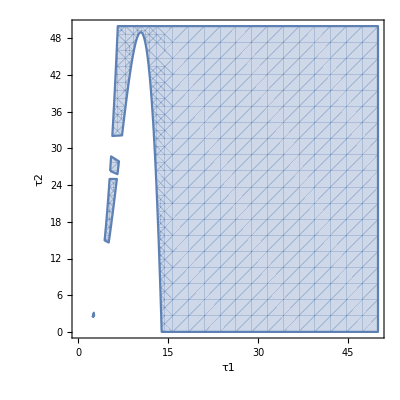

```mathematica
(*Visualize feasible region*)
params={σamax->0.3,σomax->4.182};
σaa=σomax/τ1-σomax^3τ2/(3τ1^4);
RegionPlot[(σaa>0&&σaa≤σamax)/.params,{τ1,0,50},{τ2,0,50},FrameLabel->{τ1,τ2}]
```